```mathematica
heqn=D[u[x,t], t]==D[u[x,t], x,x];
```

```mathematica
ic=u[x,0]==Sin[π x];
```

```mathematica
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
```

ⅇ^(-π^2 t) Sin[π x]

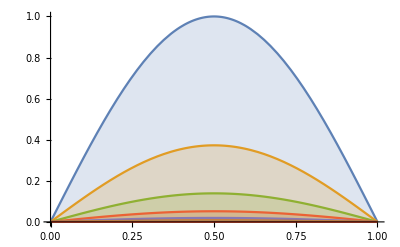

```mathematica
Plot[Evaluate[Table[sol,{t,0,1,0.1}]],{x,0,1},PlotRange->All,Filling->Axis]
```